```mathematica
(* From k0/H To amp,factor (ineffecient) *)
(* ------------------------------------ *)
(* parameter input *)
(*
phi1=4.3387189;
phid1=0.51552635;
alf1=3.3*6.7;
hubble1 = Sqrt[(phid1^2+phi1^2+2.*0.996*phi1*Sin[3.3*phi1]/3.3)/6.]
*)

phi1=4.4273861;
phid1=0.36180591;
alf1=3.3*6.7;
hubble1 = Sqrt[(phid1^2+phi1^2+2.*0.996*phi1*Sin[3.3*phi1]/3.3)/6.]

(*
phi1=4.5042820;
phid1=0.24034564;
alf1=3.3*6.7;
hubble1 = Sqrt[(phid1^2+phi1^2+2.*0.996*phi1*Sin[3.3*phi1]/3.3)/6.]
*)
(*
phi1=4.5929167;
phid1=0.12242202;
alf1=3.3*6.7;
hubble1 = Sqrt[(phid1^2+phi1^2+2.*0.996*phi1*Sin[3.3*phi1]/3.3)/6.]
*)
(*
phi1=4.6205366;
phid1=0.092055699;
alf1=3.3*6.7;
hubble1 = Sqrt[(phid1^2+phi1^2+2.*0.996*phi1*Sin[3.3*phi1]/3.3)/6.]
*)
(*
phi1=5.0;
phid1=0.80655;
alf1=25.;
hubble1=Sqrt[(phi1^2+phid1^2)/6.];
*)
(*
phi1=14.5;
phid1=0.8152128;
alf1=42.;
hubble1=Sqrt[(phi1^2+phid1^2)/6.];
*)

xi1=alf1*phid1/(2.*hubble1)

(* import keff *)
kefflist=Import["/Users/tsuchitashunsuke/Dropbox/lattice/coulomb/CWFvalue/bumpy/64/H=1.92/L=3.5/x0_list.dat","List"]
Length[kefflist]

(* calculate CWF and output *)

(* grow amplitude *)
cwflist=Function[x,If[x==0.,0.,Sqrt[(CoulombF[0,xi1,x])^2+(CoulombG[0,xi1,x])^2]]]/@kefflist;
Length[cwflist]
Export["/Users/tsuchitashunsuke/Dropbox/lattice/coulomb/CWFvalue/bumpy/64/H=1.92/L=3.5/growAmp.dat",cwflist,"List"]

(* grow factor *)
cwflist=Function[x,If[x==0.,0.,(CoulombG[0,xi1,x]*CoulombG[1,xi1,x]+CoulombF[0,xi1,x]*CoulombF[1,xi1,x])/((CoulombF[0,xi1,x])^2+(CoulombG[0,xi1,x])^2)]]/@kefflist;
Length[cwflist]
Export["/Users/tsuchitashunsuke/Dropbox/lattice/coulomb/CWFvalue/bumpy/64/H=1.92/L=3.5/growFac.dat",cwflist,"List"]

(* stable amplitude *)
cwflist=Function[x,If[x==0.,0.,Sqrt[(CoulombF[0,-xi1,x])^2+(CoulombG[0,-xi1,x])^2]]]/@kefflist;
Length[cwflist]
Export["/Users/tsuchitashunsuke/Dropbox/lattice/coulomb/CWFvalue/bumpy/64/H=1.92/L=3.5/stabAmp.dat",cwflist,"List"]

(* stable factor *)
cwflist=Function[x,If[x==0.,0.,(CoulombG[0,-xi1,x]*CoulombG[1,-xi1,x]+CoulombF[0,-xi1,x]*CoulombF[1,-xi1,x])/((CoulombF[0,-xi1,x])^2+(CoulombG[0,-xi1,x])^2)]]/@kefflist;
Length[cwflist]
Export["/Users/tsuchitashunsuke/Dropbox/lattice/coulomb/CWFvalue/bumpy/64/H=1.92/L=3.5/stabFac.dat",cwflist,"List"]
```

1.9197

2.08354

131076

131076

/Users/tsuchitashunsuke/Dropbox/lattice/coulomb/CWFvalue/bumpy/64/H=1.92/L=3.5/growAmp.dat

131076

/Users/tsuchitashunsuke/Dropbox/lattice/coulomb/CWFvalue/bumpy/64/H=1.92/L=3.5/growFac.dat

131076

/Users/tsuchitashunsuke/Dropbox/lattice/coulomb/CWFvalue/bumpy/64/H=1.92/L=3.5/stabAmp.dat

131076

/Users/tsuchitashunsuke/Dropbox/lattice/coulomb/CWFvalue/bumpy/64/H=1.92/L=3.5/stabFac.dat

1.9197

2.08354

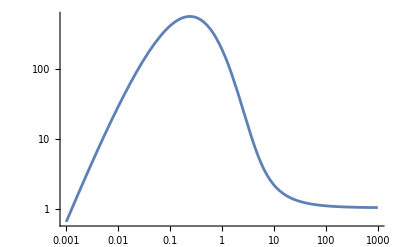

459.716

```mathematica
(* Comfirmation *)
(* ------------------------------------ *)
(* parameter input *)
(*
phi=4.3;
phid=0.5;
alf=3.3*6.7;
hubble=1.9;
*)
(*
phi=4.6205366;
phid=0.092055699;
alf=3.3*6.7;
hubble=1.9406;
*)
(*
phi=4.5042820;
phid=0.24034564;
alf=3.3*6.7;
hubble= Sqrt[(phid^2+phi^2+2.*0.996*phi*Sin[3.3*phi]/3.3)/6.]
*)
phi=4.4273861;
phid=0.36180591;
alf=3.3*6.7;
hubble = Sqrt[(phid1^2+phi1^2+2.*0.996*phi1*Sin[3.3*phi1]/3.3)/6.]
(*
phi=5.5;
phid=0.80815;
alf=25.;
hubble=Sqrt[(phi^2+phid^2)/6.]
*)
(*
phi=14.5;
phid=0.8152128;
alf=42.;
hubble=Sqrt[(phi^2+phid^2)/6.]
*)
xi=alf*phid/(2.*hubble)

(* graph *)
(*
min=0;
max=130;
Plot[Sqrt[(CoulombF[0,xi,x])^2+(CoulombG[0,xi,x])^2],{x,min,max}]
Plot[(CoulombG[0,xi,x]*CoulombG[1,xi,x]+CoulombF[0,xi,x]*CoulombF[1,xi,x])/((CoulombF[0,xi,x])^2+(CoulombG[0,xi,x])^2),{x,min,max}]
Plot[Sqrt[(CoulombF[0,-xi,x])^2+(CoulombG[0,-xi,x])^2],{x,min,max}]
Plot[(CoulombG[0,-xi,x]*CoulombG[1,-xi,x]+CoulombF[0,-xi,x]*CoulombF[1,-xi,x])/((CoulombF[0,-xi,x])^2+(CoulombG[0,-xi,x])^2),{x,min,max}]
*)
(* background back reaction *)
amp1[x_]:=Sqrt[1+xi^2]*(CoulombF[0,xi,x]*CoulombF[1,xi,x]+CoulombG[0,xi,x]*CoulombG[1,xi,x])
amp2[x_]:=(xi+1/x)*(CoulombF[0,xi,x]*CoulombF[0,xi,x]+CoulombG[0,xi,x]*CoulombG[0,xi,x])
(*
Plot[amp1[x],{x,0.01,100}]
Plot[amp2[x],{x,0.01,100}]
LogLogPlot[-amp2[x]+amp1[x],{x,0.001,100}]
*)
LogLogPlot[x^2*(-amp2[x]+amp1[x]),{x,0.001,1000}]
NIntegrate[x^2*(-amp2[x]+amp1[x]),{x,0.1,2}]

(* value comfirmation *)
(*
inputvalue=11.034269439581;
Function[x,Sqrt[(CoulombF[0,xi,x])^2+(CoulombG[0,xi,x])^2]][inputvalue]
Function[x,(CoulombG[0,xi,x]*CoulombG[1,xi,x]+CoulombF[0,xi,x]*CoulombF[1,xi,x])/((CoulombF[0,xi,x])^2+(CoulombG[0,xi,x])^2)][inputvalue]
Function[x,Sqrt[(CoulombF[0,-xi,x])^2+(CoulombG[0,-xi,x])^2]][inputvalue]
Function[x,(CoulombG[0,-xi,x]*CoulombG[1,-xi,x]+CoulombF[0,-xi,x]*CoulombF[1,-xi,x])/((CoulombF[0,-xi,x])^2+(CoulombG[0,-xi,x])^2)][inputvalue]
*)
```

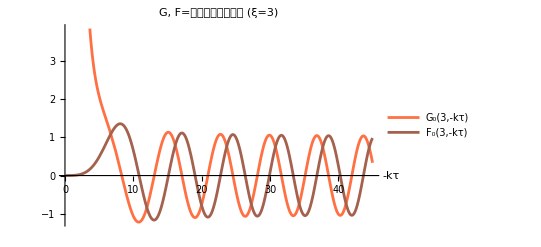

/Users/tsuchitashunsuke/Desktop/cwf.png

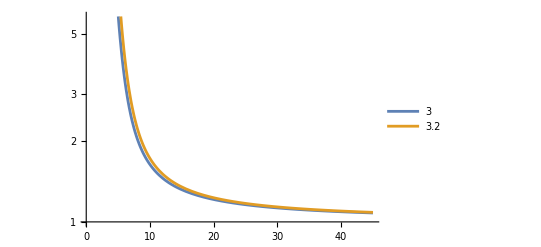

```mathematica
(* Image of Coulomb Wave Function *)
xi=3;
LL=Plot[{CoulombG[0,xi,x],CoulombF[0,xi,x]},{x,0.1,45},AxesLabel->{Style["-kτ",Italic],None},PlotLabel->Style["G, F=クーロン波動関数  (ξ=3)",Italic],LabelStyle->{GrayLevel[0]},PlotLegends->{Row[{Subscript["G","0"],"(","3",",","-kτ",")"}],Row[{Subscript["F","0"],"(","3",",","-kτ",")"}]},PlotStyle->{RGBColor[1,0.439,0.263],RGBColor[0.643,0.380,0.306]}]
Export["/Users/tsuchitashunsuke/Desktop/cwf.png",LL,"PNG"]
LL=LogPlot[{(CoulombG[0,xi,x])^2+(CoulombF[0,xi,x])^2,(CoulombG[0,xi+0.2,x])^2+(CoulombF[0,xi+0.2,x])^2},{x,0.1,45},PlotLegends->{xi=3,xi=3.2}]
```

```mathematica
Export["/Users/tsuchitashunsuke/Desktop/fig.png",LL,"PNG"]
```

/Users/tsuchitashunsuke/Desktop/fig.png

```mathematica
Export["/Users/tsuchitashunsuke/Desktop/cwf.png",%36,"PNG"]
```

/Users/tsuchitashunsuke/Desktop/cwf.png